0.00801386

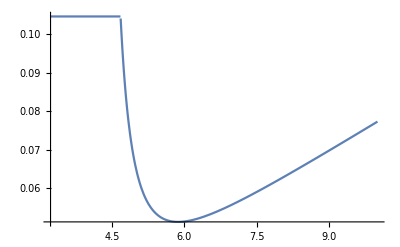

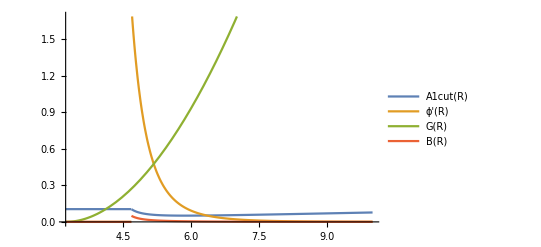

```mathematica
α=0.0077;
a=3.23;
T=1;
μ=2.3;
σ=1;
n=136;
rcut:= 4.68;    
c=n/(4/3*Pi*a^3);
L=((4*Pi*σ^6*c)/(12*T)*2)^(1/3);
A1[R_]:=α*a*(Exp[(2*(L/σ)^3)/(R-a)^3]-1+R/a);
A1cut[R_]:=Piecewise[{{A1[rcut],R≤rcut},{A1[R],R>rcut}}];
Ω[R_]:=-a/R*(2/(R/a+1)^3+2/(R/a-1)^3+1/(R/a+1)^2-1/(R/a-1)^2);
omegacut[R_]:=Piecewise[{{Ω[rcut],R≤rcut},{Ω[R],R>rcut}}];
ϕ[R_]:=(L/(σ*a))^3*omegacut[R];
G[R_]:=((a/(2*R))-((3*R)/(2*a))+(R/a)^2)
B[R_]:=G[R]*A1cut[R]*ϕ'[R];
Vx=(2*a*T)/(9*μ)*NIntegrate[B[R],{R,a,Infinity}]
Plot[A1cut[R],{R,3.23,10}]
Plot[{A1cut[R],ϕ'[R],G[R],B[R]},{R,a,10},PlotLegends->"Expressions"]
```

```mathematica
FindMinimum[A1[R],{R,5} ]
```

```mathematica
Limit[A1[R],R->a]
```

∞

```mathematica
ϕ'[R]
```

```mathematica
(0.19341773848789762 (2/(-1+0.30959752321981426 R)^3-1/(-1+0.30959752321981426 R)^2+2/(1+0.30959752321981426 R)^3+1/(1+0.30959752321981426 R)^2))/R^2-
Limit[ϕ'[R],R->a]
```

-∞

```mathematica
Limit[G[R],R->Infinity]
```

∞

```mathematica
Limit[G[R]*A1[R]*ϕ'[R],R->a]
```

∞

```mathematica
Limit[A1[R]*ϕ'[R],R->Infinity]
```

0.

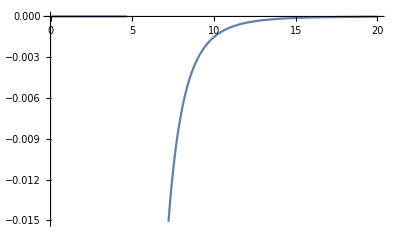

```mathematica
Plot[ϕ[R],{R,0,20}]
```

```mathematica
Plot[A1[R],{R,3.23,5}]
```

-Graphics-